```mathematica
cloud1 = Import["D:\\FIZYKA\\LICENCJAT\\rozpad beta 6He\\diffusion\\dyfuzja 6He z pulpitu win\\dane z eksperymentu\\cloud1.dat"];
cloud2 = Import["D:\\FIZYKA\\LICENCJAT\\rozpad beta 6He\\diffusion\\dyfuzja 6He z pulpitu win\\dane z eksperymentu\\cloud2.dat"];
data=Import["D:\\FIZYKA\\LICENCJAT\\rozpad beta 6He\\diffusion\\dyfuzja 6He z pulpitu win\\dane z eksperymentu\\TEST.dat"];
cloud1=Select[data,#[[3]]≤ 150/0.635&]*0.635;
cloud2=Select[data,#[[3]]> 150/0.635&]*0.635;
```

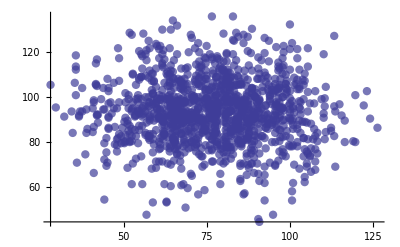

```mathematica
cl1x=cloud1[[;;,2]];
cl1z=cloud1[[;;,3]];
cl1=Transpose@{cl1z,cl1x};
pl1=ListPlot[cl1,PlotStyle->{AbsolutePointSize[6],Opacity[0.7]}]
```

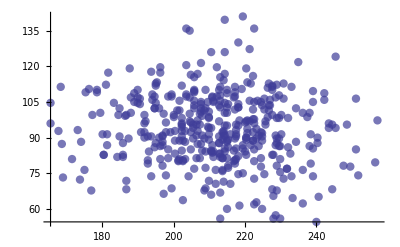

```mathematica
cl2x=cloud2[[;;,2]];
cl2z=cloud2[[;;,3]];
cl2=Transpose@{cl2z,cl2x};
pl2=ListPlot[cl2,PlotStyle->{AbsolutePointSize[6],Opacity[0.7]}]
```

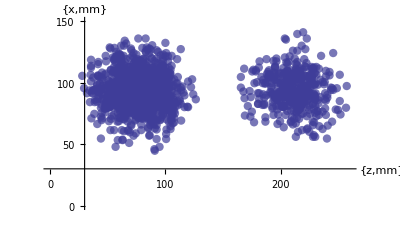

```mathematica
Show[pl1,pl2,PlotRange-> {{0,260},{0,150}},AxesLabel->{{z,mm},{x,mm}},BaseStyle->{FontSize->12},AxesOrigin->{30,30},AspectRatio->Automatic,Ticks->{{0,50,100,150,200,250},{0,50,100,150}}]
(*PlotLabel-> "Położenia rozpadów zarejestrowanych w detektorze OTPC",*)
(*FontWeight->"Bold"*)
```

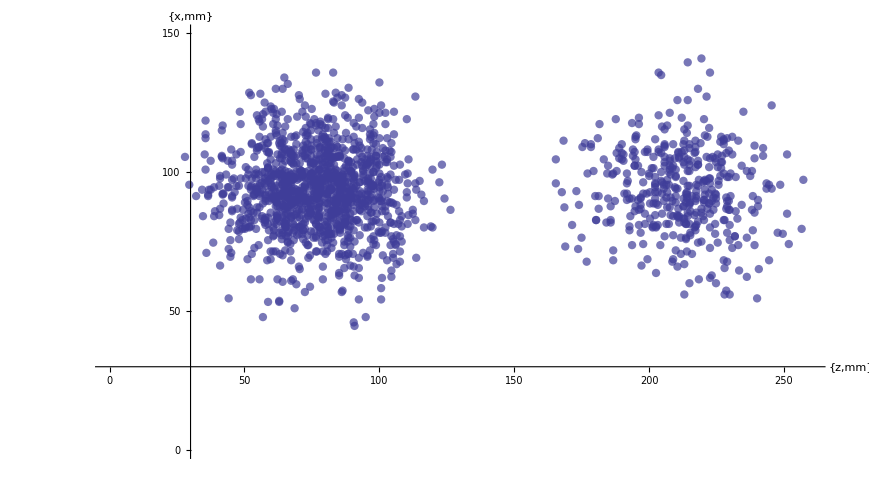

```mathematica
Show[%128,ImageSize->Large]
```

```mathematica
Export["chmury ALL scaling.jpg",%129,"JPEG"]
```

chmury ALL scaling.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["chmury ALL scaling.jpg"]]]
```

```mathematica
Export["chmury ALL scaling",%129,"JPEG"]
```

chmury ALL scaling